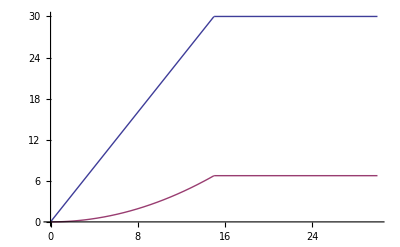

```mathematica
m=1500; (*Massa auto in kg*)
vmax=30; (*Eindsnelheid in m/s*)
a=;(*Versnelling in m/2^2*)
v[t_]:=Piecewise[{{a*t, t<15}, {30, t≥15}}];
Ek[t_]:=1/2 m*v[t]^2;
Plot[{v[t],Ek[t]/100000},{t,0,30}]
```

P = F*v;
F=m*a;

```mathematica
m=1500;
vData={{0,0},{5,10},{10,8},{20,0}};
adata[t_]:=Table[{(vData[[i,2]]-vData[[i-1,2]])/(vData[[i,1]]-vData[[i-1,1]])(t-vData[[i-1,1]])+vData[[i-1,2]],vData[[i-1,1]]<t<=vData[[i,1]]},{i,2,Length[vData]}]
```

```mathematica
adata[t]
```

{{2 t,0<t≤5},{10-2/5 (-5+t),5<t≤10},{8-4/5 (-10+t),10<t≤20}}

```mathematica
v[t_]:=Piecewise[adata[t]]
```

```mathematica
v[t]
```

Piecewise[{{2 t, 0<t≤5}, {10-2/5 (-5+t), 5<t≤10}, {8-4/5 (-10+t), 10<t≤20}, {0, True}}]

```mathematica
a[t_]:=D[v[t],t]
```

General::ivar: 1.00039 is not a valid variable.

General::ivar: 1.38814 is not a valid variable.

General::ivar: 1.7759 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

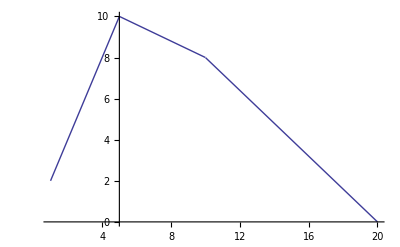

```mathematica
Plot[{v[t],a[t]},{t,1,20}]
```

```mathematica
v[3]
```

6

```mathematica
Line
```

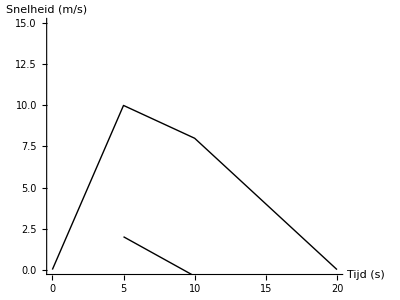

```mathematica
Graphics[{Line[vData],Line[aData]},Axes->True,AxesLabel->{"Tijd (s)","Snelheid (m/s)"},PlotRange->{0,15}]
```

```mathematica
vData[[2,2]]
```

10